{{0.307487,-5.73494},{0.320856,-5.47289},{0.336898,-5.15663},{0.360963,-4.80422},{0.379679,-4.53313},{0.395722,-4.30723},{0.417112,-4.05422},{0.454545,-3.64759},{0.513369,-3.15964},{0.548128,-2.91566},{0.585561,-2.68072},{0.631016,-2.46386},{0.679144,-2.23795},{0.73262,-2.03916},{0.791444,-1.85843},{0.852941,-1.69578},{0.919786,-1.54217},{0.986631,-1.39759},{1.05615,-1.28916},{1.12834,-1.17169},{1.20588,-1.09036},{1.28075,-1.00904},{1.35561,-0.945783},{1.43316,-0.873494},{1.5107,-0.819277},{1.58824,-0.76506},{1.66578,-0.71988},{1.74332,-0.683735},{1.82353,-0.64759},{1.90374,-0.611446},{1.98128,-0.575301},{2.05882,-0.566265},{2.13904,-0.53012},{2.21925,-0.503012},{2.29679,-0.48494},{2.37433,-0.475904},{2.45455,-0.448795},{2.53476,-0.439759},{2.6123,-0.421687},{2.77005,-0.394578},{2.92781,-0.36747},{3.13369,-0.331325},{3.35561,-0.304217}}

-0.0183934-0.965545/r-(1.08212 ⅇ^-r)/r

-0.0183934-0.965545/r-(1.08212 ⅇ^-r)/r

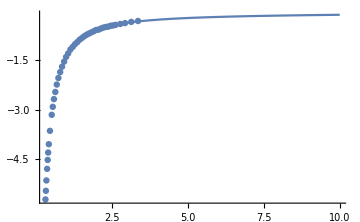

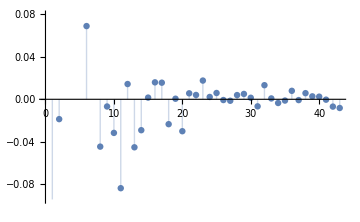

```mathematica
TrueV=Import["C:\\Users\\ASUS\\Documents\\Lepage_TrueV.dat","CSV"]
(*V=Interpolation[TrueV](*Fit[TrueV,{1,1/r,E^(-a r)},r]*)*)
v=Fit[TrueV,{1,1/r(*,1/r^2*)(*,Erf[r]*)(*,1/r^3*)(*,r,r^2*)(*,E^-r*)(*,E^r*)(*,E^(-2r)*)(*,E^(2r)*),E^-r/r(*,E^(-2r)/r*)},r]
V[r_]=v
Show[ListPlot[TrueV],Plot[V[r],{r,0.01,10}],ImageSize->Medium,PlotRange->{{0,10},{0,-6}}]
ListPlot[Table[(Transpose[TrueV][[2]][[i]])^2-(V[r]/.r->Transpose[TrueV][[1]][[i]])^2,{i,43}],ImageSize->Medium,Filling->Axis]
(*Show[ListPlot[TrueV],Plot[f[r],{r,0.307,3.5}],ImageSize->Large]*)
```

```mathematica
#/.FindFit[TrueV,#,{a,b,c,d,e},r]&[-1/r+c E^(-d r)/r+a/r^b]
```

-1/r-(1.03651 ⅇ^(-1.06528 r))/r-0.0246312/r^0.839158

```mathematica
ModelV:=-1/r+c E^(-d r)/r
ModelV1:=-a/r^b+c E^(-d r)/r
ModelV2:=-1/r+a/r^b
FindFit[TrueV,ModelV,{a,b,c,d},r]
FindFit[TrueV,ModelV1,{a,b,c,d},r]
FindFit[TrueV,ModelV2,{a,b,c,d},r]
```

{a→1.,b→1.,c→-1.04152,d→0.9991}

{a→1.00409,b→0.976102,c→-1.09835,d→1.06921}

{a→-0.393006,b→1.59937,c→1.,d→1.}

```mathematica
V2[r_]=ModelV/.%%%
V1[r_]=ModelV1/.%%%
V[r_]=ModelV2/.%%%
```

-1/r-(1.04152 ⅇ^(-0.9991 r))/r

-(1.09835 ⅇ^(-1.06921 r))/r-1.00409/r^0.976102

-0.393006/r^1.59937-1/r

```mathematica
-1.3862179318475605/r^1.2152447118079408/.r->0.3074866310160428
```

-5.81096

```mathematica
Table[V[r]/.r->Transpose[TrueV][[1]][[i]],{i,43}]
```

{-5.7488,-5.47651,-5.17888,-4.78315,-4.5109,-4.29861,-4.0417,-3.65214,-3.15877,-2.91906,-2.69428,-2.45906,-2.24633,-2.04487,-1.85695,-1.69039,-1.53681,-1.40603,-1.28941,-1.18522,-1.08888,-1.00836,-0.937955,-0.873902,-0.817415,-0.767307,-0.72262,-0.682572,-0.645338,-0.611788,-0.582395,-0.555612,-0.530316,-0.507179,-0.486627,-0.46766,-0.449526,-0.432744,-0.417672,-0.390054,-0.365894,-0.338582,-0.31343}

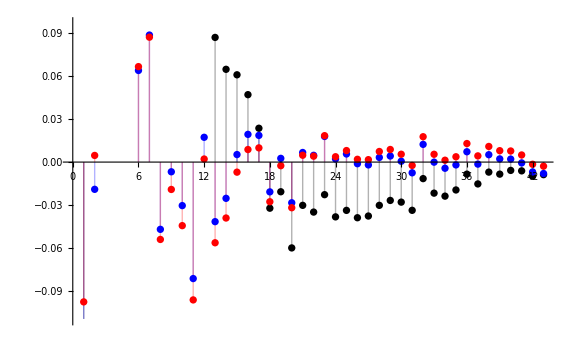

```mathematica
ListPlot[{Table[(Transpose[TrueV][[2]][[i]])^2-(V[r]/.r->Transpose[TrueV][[1]][[i]])^2,{i,43}],Table[(Transpose[TrueV][[2]][[i]])^2-(V1[r]/.r->Transpose[TrueV][[1]][[i]])^2,{i,43}],Table[(Transpose[TrueV][[2]][[i]])^2-(V2[r]/.r->Transpose[TrueV][[1]][[i]])^2,{i,43}]},ImageSize->Large,Filling->Axis,PlotStyle->{Black,Blue,Red}]
```

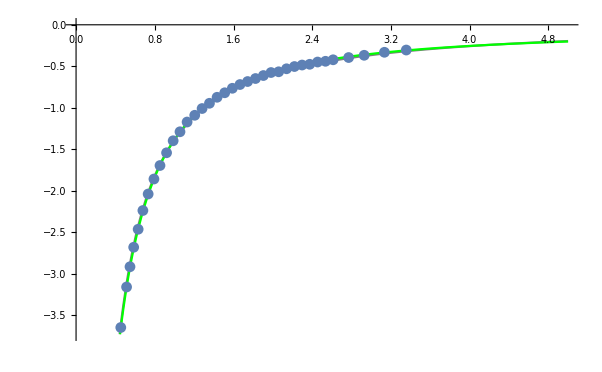

```mathematica
Show[Plot[{V[r],V2[r]},{r,0,5},PlotStyle->{Gray,Green}],ListPlot[TrueV]]
```

```mathematica
V[r]
```

-1/r-(1.04152 ⅇ^(-0.9991 r))/r

```mathematica
α=2.;u0=1.*10^-8;
f[e_?NumberQ(*/;e∈Reals*)]:=
Block[{u,r,r1=1500.,r2=u0},
First[u[r2]/.
NDSolve[{u''[r]+(α(e-V[r])-0/r^2)u[r]==0,u[r1]==u0,u'[r1]==(*√(α(V[r1]-e)) u0*)-u0},
u,{r,r1,r2},Method->"Chasing",MaxSteps->Infinity,WorkingPrecision->20,MaxStepFraction->10^-3]]]
ew={
FindRoot[f[e]==0,{e,-0.22,-0.2},MaxIterations->1000,WorkingPrecision->20],
FindRoot[f[e]==0,{e,-0.15,-0.1},MaxIterations->1000,WorkingPrecision->20],
FindRoot[f[e]==0,{e,-0.1,-0.05}],
FindRoot[f[e]==0,{e,-0.6,-0.04}],
FindRoot[f[e]==0,{e,-0.05,-0.02},MaxIterations->1000,WorkingPrecision->20],
FindRoot[f[e]==0,{e,-0.02,-0.01}],
FindRoot[f[e]==0,{e,-0.010,-0.005}],
FindRoot[f[e]==0,{e,-0.005,-0.003}],
FindRoot[f[e]==0,{e,-0.002,-0.001}],
FindRoot[f[e]==0,{e,-0.001,-0.0007}],
FindRoot[f[e]==0,{e,-0.0007,-0.0005}],
FindRoot[f[e]==0,{e,-0.0005,-0.0003}],
FindRoot[f[e]==0,{e,-0.0003,-0.0002}],
FindRoot[f[e]==0,{e,-0.0002,-0.0001}],
FindRoot[f[e]==0,{e,-0.0001,-0.00007}],
FindRoot[f[e]==0,{e,-0.00007,-0.00005}],
FindRoot[f[e]==0,{e,-0.00005,-0.00003}],
FindRoot[f[e]==0,{e,-0.00003,-0.00002}],
FindRoot[f[e]==0,{e,-0.00002,-0.00001}],
FindRoot[f[e]==0,{e,-0.00001,-0.000007}],
FindRoot[f[e]==0,{e,-0.000007,-0.000005}],
FindRoot[f[e]==0,{e,-0.000005,-0.000003}],
FindRoot[f[e]==0,{e,-0.000003,-0.000002}],
FindRoot[f[e]==0,{e,-0.000002,-0.000001}],
FindRoot[f[e]==0,{e,-0.000001,-0.0000005}]
}//AbsoluteTiming
```

NDSolve::precw: 参数函数的精度 ({{2. (-0.22+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (-0.2+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (-0.22000000000000000111+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::cvmit: 无法在 1000 次迭代中收敛到要求的准确度或者精度.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

FindRoot::cvmit: 无法在 1000 次迭代中收敛到要求的准确度或者精度.

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，FindRoot::cvmit 的进一步输出将被抑制.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

General::stop: 在本次计算中，FindRoot::brmp 的进一步输出将被抑制.

{3681.92,{{e→-0.090785655010884447413},{e→-0.10000000000000000555},{e→-0.0907857},{e→-0.25172},{e→-0.020000000000000000416},{e→-0.01},{e→-0.00957401},{e→-0.00481071},{e→-0.00123293},{e→-0.000672704},{e→-0.000533096},{e→0.000442744},{e→-0.000264886},{e→-0.000161842},{e→-0.0000524727},{e→-0.000052473},{e→-0.0000524699},{e→-0.0000524727},{e→-0.0000524731},{e→0.0000627991},{e→-0.0000524731},{e→-0.000161842},{e→-0.000161842},{e→-0.0000524727},{e→-0.0000524727}}}

```mathematica
Flatten[ew]
```

{1708.06,e→-0.20206474355063304283,e→-0.10000000000000000555,e→-0.061015,e→-0.025816354438023567987,e→-0.0131841,e→-0.00759374,e→-0.00221145,e→-0.000917526,e→-0.000717949,e→-0.000571995,e→-0.000462852,e→-0.000184601,e→-0.0000875686,e→-0.0000875686,e→-0.0000875686,e→-0.000028224,e→-0.0000282228,e→-0.0000282228,e→-0.0000282228,e→-0.0000282228,e→-0.0000282228,e→-0.0000282228,e→-0.0000282226,e→-0.0000282228}

```mathematica
{677.9072250486088,{{e->-0.2020647435991993588121597437980620898693963357079478998528`20.},{e->-0.1000000000000000055511151231257827021181583404541015624955`20.},{e->-0.06101504061183388},{e->-0.03},{e->-0.013184085186119436},{e->-0.007593739341062496},{e->-0.0022114451374815975},{e->-0.0009143326733276428},{e->-0.0009143326723454164},{e->-0.0006727397261354283},{e->-0.0003877160629115215},{e->-0.0006727455497889054},{e->-0.00004060308612934824},{e->-0.00004060334227290222},{e->-0.0000406033719650039},{e->-0.00004060333968047317},{e->-0.00004060342182560972},{e->-0.000040603564734534056}}}
```

{677.907,{{e→-0.20206474359919935881},{e→-0.10000000000000000555},{e→-0.061015},{e→-0.03},{e→-0.0131841},{e→-0.00759374},{e→-0.00221145},{e→-0.000914333},{e→-0.000914333},{e→-0.00067274},{e→-0.000387716},{e→-0.000672746},{e→-0.0000406031},{e→-0.0000406033},{e→-0.0000406034},{e→-0.0000406033},{e→-0.0000406034},{e→-0.0000406036}}}

```mathematica
Flatten[ew]
```

{650.504,e→-0.20206474359919935881,e→-0.10000000000000000555,e→-0.061015,e→-0.03,e→-0.0131841,e→-0.00759374,e→-0.00221145,e→-0.00221145,e→-0.000914333}

```mathematica
{1536.7185053141175,{{e->-0.2020628193297541014689817283742766951022558592849679852761`20.},{e->-0.1000000000000000055511151231257827021181583404541015624978`20.},{e->-0.06101464728233512},{e->-0.03},{e->-0.025816228526366253}}}[[2]]
```

{{e→-0.20206281932975410147},{e→-0.10000000000000000555},{e→-0.0610146},{e→-0.03},{e→-0.0258162}}

```mathematica
{1288.9406037336767,{{e->-0.2020628193247130810978538837096073464283266689922558931338`20.},{e->-0.1000000000000000055511151231257827021181583404541015624971`20.},{e->-0.06101464728141968},{e->-0.025816228530248245},{e->-0.025816228530248245}}}[[2]](*Prof.Jia*)
```

{{e→-0.2020628193247130811},{e→-0.10000000000000000555},{e→-0.0610146},{e→-0.0258162},{e→-0.0258162}}

```mathematica
{32.25810747786332,{{e->-1.3373052792128256352059755219691467564294034203964312350024`20.},{e->-0.1864329749305319098021614432316324710515216684009185330101`20.},{e->-0.07105724406592276},{e->-0.03740708525517129},{e->-0.023050931457661874}}}[[2]](*only additional Exp*)
```

{{e→-1.3373052792128256352},{e→-0.1864329749305319098},{e→-0.0710572},{e→-0.0374071},{e→-0.0230509}}

```mathematica
{39.21444829081163,{{e->-1.334501821908841956736047087475520284087476837506850122106`20.},{e->-0.1936564247377447990539694935096284390175786915884934148768`20.},{e->-0.07688480905045168},{e->-0.04159371156656489},{e->-0.026174841951916918}}}[[2]](*different 1/r Exp*)
```

{{e→-1.3345018219088419567},{e→-0.19365642473774479905},{e→-0.0768848},{e→-0.0415937},{e→-0.0261748}}

```mathematica
Clear["Global`*"]
```